# Confronti modello di cupola Nel seguito verranno confrontati i risultati ottenuti da tre diversi modelli che descrivono il comportamento della cupola a tutt sesto. Il confronto verrà fatto tra il modello di cupola di Geckeler, il modello COMPLETO di cupola monodimensionale e i miei due modelli di cupola monodimensionale.

```mathematica
r1[s_]=R;
r2[s_]=R;
```

```mathematica
pn[s_]=P Sin[s/R];
```

```mathematica
pt[s_]=P Cos[s/R];
```

## EQUAZIONI INESTENSIBILI ANALITICHE

#### Equazioni di congruenza

```mathematica
v10[s_]=-R u10'[s];
φ10[s_]=v10'[s]-u10[s]/R;
κm10[s_]=φ10'[s];
ϵp10[s_]=v10[s]/R;
```

#### Legame

```mathematica
Nm10[s_]=R(P Sin[s/R]+Tm10'[s]-Np10[s]/R);
```

```mathematica
Tm10[s_]=-Mm10'[s];
```

```mathematica
Mm10[s_]=El κm10[s];
```

```mathematica
Np10[s_]= +EA ϵp10[s];
```

```mathematica
a=-1/R^2;
```

```mathematica
(*b=(√EA)/(R √El);*)
```

```mathematica
b=(2 √3)/(h R);
```

```mathematica
(*b=√3;*)
```

```mathematica
α=√(a-ⅈ b);
```

```mathematica
(*α=√(-ⅈ b);*)
```

```mathematica
β=√(a+ⅈ b);
```

```mathematica
(*β=√(ⅈ b);*)
```

```mathematica
u10[s_]=1/α^2(ⅇ^(α s)C[1]+ⅇ^(-α s)C[2])+1/β^2(ⅇ^(β s)C[3]+ⅇ^(-β s)C[4])+C[5]+s C[6]+(2 P R^2 Cos[s/R])/EA;
```

## EQUAZIONI MIE NON INESTENSIBILI

#### Equazioni di congruenza

```mathematica
ϵm6[s_]=u6'[s]+v6[s]/r1[s];
φ6[s_]=v6'[s]-u6[s]/r1[s];
κm6[s_]=φ6'[s];
ϵp6[s_]=v6[s]/r2[s];
```

#### Legame

```mathematica
Nm6[s_]=EA ϵm6[s];
```

```mathematica
Tm6[s_]=-Mm6'[s];
```

```mathematica
Mm6[s_]=El κm6[s];
```

```mathematica
Np6[s_]= +EA ϵp6[s];
```

#### Equilibrio

```mathematica
EQ1=-Nm6'[s]-Tm6[s]/r1[s]==pt[s];
```

```mathematica
EQ2=Nm6[s]/r1[s]-Tm6'[s]+Np6[s]/r2[s]==pn[s];
```

```mathematica
SOL=DSolve[{EQ1},{u6[s]},s]

u6[s_]=u6[s]/.SOL[[1]];
```

{{u6[s]→C[1]+s C[2]+∫_1^s -(R (P R^2 Sin[K[1]/R]+EA v6[K[1]]-El v6''[K[1]]))/(El+EA R^2)ⅆK[1]}}

```mathematica
SOL=DSolve[{EQ2},{v6[s]},s];
```

```mathematica
v6[s_]=v6[s]/.SOL[[1]]
```

ⅇ^(√(-1/R^2-(√(-El R^4 (El+EA R^2)))/(El R^4)) s) C[3]+ⅇ^(-√(-1/R^2-(√(-El R^4 (El+EA R^2)))/(El R^4)) s) C[4]+ⅇ^(√(-1/R^2+(√(-El R^4 (El+EA R^2)))/(El R^4)) s) C[5]+ⅇ^(-√(-1/R^2+(√(-El R^4 (El+EA R^2)))/(El R^4)) s) C[6]+(R (-EA El C[2]-EA^2 R^2 C[2]+4 El P R Sin[s/R]+2 EA P R^3 Sin[s/R]))/(EA (2 El+EA R^2))

## DATI

```mathematica
θ0=π/6; (*θ0 è l'angolo di ribassamento della cupola*)
α0=θ0;
θmax=π/2-θ0;
```

```mathematica
h=0.25;
R=10;
γ=25;
p[θ_]=-γ h;
EL=3×10^7;
ν=0.3;
G=EL/(2(1+ν));
El=(EL h^3)/(12(1-ν^2));
EA=(EL h)/(1-ν^2);
α=π/2-0.01;
```

```mathematica
P=-γ h;
```

## EQUAZIONI REISSNER

```mathematica
r00[s_]=R Cos[s/R];
```

#### Equazioni di congruenza

```mathematica
ϵm7[s_]=u7'[s]+v7[s]/R
 γm7[s_]=v7'[s]-φ7[s]-u7[s]/R
 κm7[s_]=φ7'[s];
ϵp7[s_]=(v7[s] Cos[s/R]-u7[s]Sin [s/R])/r00[s];
κp7[s_]=(φ7[s] Sin[s/R])/r00[s];
```

v7[s]/10+u7'[s]

-u7[s]/10-φ7[s]+v7'[s]

#### Legame

```mathematica
Nm7[s_]= (EL h)/(1-ν^2)ϵm7[s]+ν(EL h)/(1-ν^2)ϵp7[s];
```

```mathematica
Tm7[s_]=5/6 G h γm7[s];
```

```mathematica
Mm7[s_]=(EL h^3)/(12(1-ν^2)) κm7[s];
```

```mathematica
Np7[s_]=(EL h)/(1-ν^2)ϵp7[s]+ν(EL h)/(1-ν^2)ϵm7[s];
```

```mathematica
Mp7[s_]=(EL h^3)/(12(1-ν^2)) κp7[s];
```

#### Equilibrio

```mathematica
EQ1=-D[Nm7[s] r00[s],s]-(Tm7[s] r00[s])/R-Np7[s] Sin[s/R]==pt[s] r00[s];
EQ2=(Nm7[s] r00[s])/R-D[Tm7[s] r00[s],s]+Np7[s] Cos[s/R]==pn[s] r00[s];
EQ3=-Tm7[s] r00[s]-D[Mm7[s] r00[s],s]+Mp7[s] Sin[s/R]==0;
```

```mathematica
EQUA={EQ1,EQ2,EQ3};
```

## SOLUZIONE EQUAZIONI DI REISSNER

```mathematica
SOLA=NDSolve[{EQUA,u7[R α0]==0,v7[R α0]==0,φ7[R α0]==0,u7[R α]==0,φ7[R α]==0,Tm7[R α]==0},{u7,v7,φ7},{s,R α0,R α},WorkingPrecision ->30 , PrecisionGoal-> 10];
```

NDSolve::precw: The precision of the differential equation ({« 1 »}) is less than WorkingPrecision (30.).

NDSolve::berr: There are significant errors {-6.87636352570312199979363935262×10^-65, « 65 », « 69 », -« 68 », -« 68 », -« 75 »} in the boundary value residuals. Returning the best solution found.

#### Spostamenti

```mathematica
u7[s_]=u7[s]/.SOLA;
```

```mathematica
v7[s_]=v7[s]/.SOLA;
```

```mathematica
φ7[s_]=φ7[s]/.SOLA;
```

#### Deformazioni

```mathematica
ϵm7[s_]=ϵm7[s]/.SOLA;
```

```mathematica
γm7[s_]=γm7[s]/.SOLA;
```

```mathematica
κm7[s_]=κm7[s]/.SOLA;
```

```mathematica
ϵp7[s_]=ϵp7[s]/.SOLA;
```

```mathematica
κp7[s_]=κp7[s]/.SOLA;
```

#### Tensioni

```mathematica
Nm7[s_]=Nm7[s]/.SOLA;
```

```mathematica
Tm7[s_]=Tm7[s]/.SOLA;
```

```mathematica
Mm7[s_]=Mm7[s]/.SOLA;
```

```mathematica
Np7[s_]=Np7[s]/.SOLA;
```

```mathematica
Mp7[s_]=Mp7[s]/.SOLA;
```

```mathematica
G1=Plot[u7[s],{s,R α0,R α},AxesOrigin->{0,0},AxesLabel->{"s","u2(s)"},PlotStyle->{Black,Dashed,Thick},PlotRange->All];
```

```mathematica
G2=Plot[v7[s],{s,R α0,R α},AxesOrigin->{0,0},AxesLabel->{"s","v2(s)"},PlotStyle->{Black,Dashed,Thick},PlotRange->All];
```

```mathematica
G3=Plot[φ7[s],{s,R α0,R α},AxesOrigin->{0,0},AxesLabel->{"s","φ2(s)"},PlotStyle->{Black,Dashed,Thick},PlotRange->All];
```

```mathematica
G4=Plot[Nm7[s],{s,R α0,R α},AxesOrigin->{0,0},AxesLabel->{"s","Nm2(s)"},PlotStyle->{Black,Dashed,Thick},PlotRange->All];
```

```mathematica
G5=Plot[Np7[s],{s,R α0,R α},AxesOrigin->{0,0},AxesLabel->{"s","Np2(s)"},PlotStyle->{Black,Dashed,Thick},PlotRange->All];
```

```mathematica
G6=Plot[Tm7[s],{s,R α0,R α},AxesOrigin->{0,0},AxesLabel->{"s","Tm2(s)"},PlotStyle->{Black,Dashed,Thick},PlotRange->All];
```

```mathematica
G7=Plot[Mm7[s],{s,R α0,R α},AxesOrigin->{0,0},AxesLabel->{"s","Mm2(s)"},PlotStyle->{Black,Dashed,Thick},PlotRange->All];
```

## Soluzione 1 - Modello di Geckeler

### Soluzione 1 - Modello di Geckeler

Il primo modello proposto è quello di Geckeler, nel quale é stato inserito il vincolo interno di indeformabilità a taglio e sono stati trascurati la cotg(θ) ed il Modulo di Poisson “ν”. Il problema viene diviso in due sottoproblemi: un problema di membrana più un problema di guscio.
Il modello non fornisce una soluzione in forma chiusa pertanto in questo caso la soluzione si ottiene solo per via numerica.

## Risoluzione del Problema di Membrana

### Dati

```mathematica
r0[θ_]=R Sin[θ];
fr[θ_]=R (1-Cos[θ]);
pn[θ_]=p[θ] Cos[θ];
pt[θ_]=p[θ] Sin[θ];
```

### Equilibrio calotta finita

```mathematica
EQ11=2π r0[θ]Nm0[θ]Sin [θ]-2π R fr[θ] p[θ]==0;
Nm0[θ_]=Nm0[θ]/.Solve[EQ11,Nm0[θ]][[1]];
```

```mathematica
Nm0[θmax]
```

-41.6667

```mathematica
Cos[θmax]
```

1/2

### Equazione di Laplace

```mathematica
EQ12=Nm0[θ]/R+Np0[θ]/R==pn[θ];
Np0[θ_]=Np0[θ]/.Solve[EQ12,Np0[θ]][[1]];
```

### Legame

```mathematica
ϵm0[θ_]=1/(EL h)(Nm0[θ]-ν Np0[θ]);
```

```mathematica
ϵp0[θ_]=1/(EL h)(Np0[θ]-ν Nm0[θ]);
```

### Campo degli spostamenti

```mathematica
u0[θ_]=Sin [θ](Integrate[ExpandAll[R((ϵm0[θ]-ϵp0[θ])/Sin[θ])],θ]+C1);
```

```mathematica
cc1=u0[θmax]==0;
```

```mathematica
C1=C1/.Solve[cc1,C1][[1]];
```

```mathematica
w0[θ_]=R ϵm0[θ]-u0'[θ];
```

### Spostamenti di bordo

```mathematica
ξ0[θ_]=u0[θ] Cos[θ]+w0[θ] Sin[θ];
```

```mathematica
η0[θ_]=-u0[θ] Sin[θ]+w0[θ] Cos[θ];
```

```mathematica
φ0[θ_]=w0'[θ]-u0[θ]/R;
```

```mathematica
ξ0[θmax]
```

0.0000264619

```mathematica
φ0[θmax]
```

0.000165988

## Grafici Pb di membrana

### Sforzo Normale di meridiano e parallelo: Nm [θ], Np [θ]

General::obspkg: "PlotLegends`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

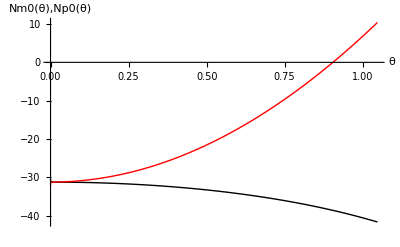

```mathematica
Needs["PlotLegends`"]
  Plot[{Nm0[θ],Np0[θ]},{θ,0,θmax},AxesOrigin->{0,0},AxesLabel->{"θ","Nm0(θ),Np0(θ)"},PlotStyle->{{Black,Thick},{Red,Thick}},PlotLegend->{"Nm0(θ)","Np0(θ)"},LegendPosition->{1,-0.8},LegendShadow->None]
```

### Deformazioni di meridiano e parallelo: ϵm [θ], ϵp [θ]

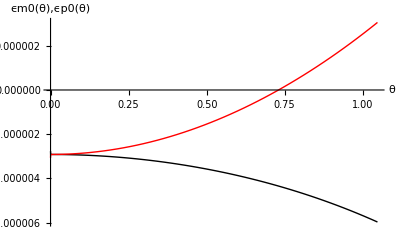

```mathematica
Plot[{ϵm0[θ],ϵp0[θ]},{θ,0,θmax},AxesOrigin->{0,0},AxesLabel->{"θ","ϵm0(θ),ϵp0(θ)"},PlotStyle->{{Black,Thick},{Red,Thick}},PlotLegend->{"ϵm0(θ)","ϵp0(θ)"},LegendPosition->{1,-0.8},LegendShadow->None]
```

### Spostamenti normali e tangenziali

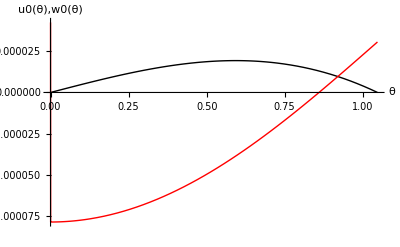

```mathematica
Plot[{u0[θ],w0[θ]},{θ,0,θmax},AxesOrigin->{0,0},AxesLabel->{"θ","u0(θ),w0(θ)"},PlotStyle->{{Black,Thick},{Red,Thick}},PlotLegend->{"u0(θ)","w0(θ)"},LegendPosition->{1,-0.8},LegendShadow->None]
```

```mathematica
u0[0]
```

Indeterminate

```mathematica
w0[0]
```

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0.  + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

Indeterminate

### Spostamenti di bordo

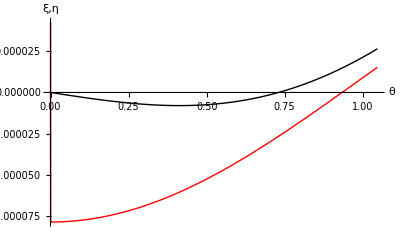

```mathematica
Plot[{ξ0[θ],η0[θ]},{θ,0,θmax},AxesOrigin->{0,0},AxesLabel->{"θ","ξ,η"},PlotStyle->{{Black,Thick},{Red,Thick}},PlotLegend->{"ξ","η"},LegendPosition->{1,-0.8},LegendShadow->None]
```

## Grandezze del pb di membrana in funzione di ω (preso dalla base alla sommità)

### Dati

```mathematica
δ=0.01;
```

```mathematica
tf=θmax;
```

```mathematica
imax=Floor[tf/δ];
```

```mathematica
F=Table[0,{imax+1},{2}];
Ft=Table[0,{imax+1},{2}];
```

### Determinazione di u0 [ω]

```mathematica
For[i=0,i≤imax,i++,F[[i+1]]={i δ,u0[i δ]}]
```

```mathematica
For[i=0,i≤imax,i++,Ft[[i+1]]={i δ+θ0,F[[imax+1-i,2]]}]
```

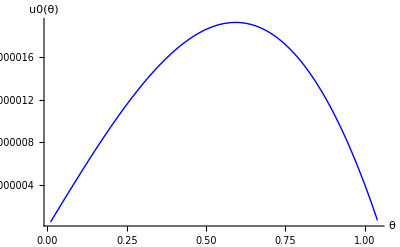

```mathematica
A1=ListLinePlot[{F}, AxesOrigin -> {0, 0}, AxesLabel -> {"θ", "u0(θ)"}, PlotStyle -> {{Blue, Thin}},PlotRange -> All]
```

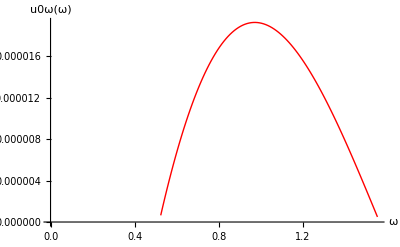

```mathematica
B1=ListLinePlot[{Ft},AxesOrigin->{0,0},AxesLabel->{"ω","u0ω(ω)"},PlotStyle->{{Red,Thin}}]
```

```mathematica
u0ω=Interpolation[Ft];
```

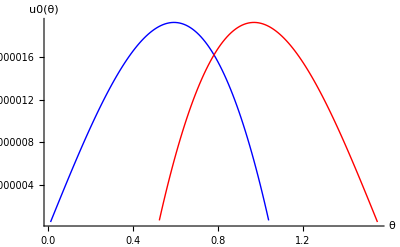

```mathematica
Show[A1,B1]
```

### Determinazione di w0 [ω]

```mathematica
For[i=1,i≤imax,i++,F[[i+1]]={i δ,w0[i δ]}]
```

```mathematica
For[i=0,i≤imax,i++,Ft[[i+1]]={i δ+θ0,F[[imax+1-i,2]]}]
```

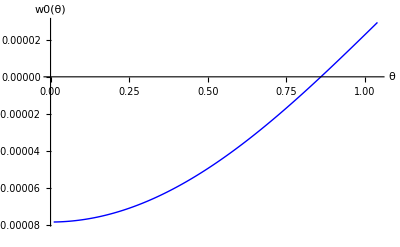

```mathematica
A2=ListLinePlot[{F},AxesOrigin->{0,0},AxesLabel->{"θ","w0(θ)"},PlotStyle->{{Blue,Thin}}]
```

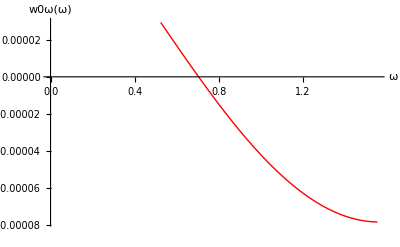

```mathematica
B2=ListLinePlot[{Ft},AxesOrigin->{0,0},AxesLabel->{"ω","w0ω(ω)"},PlotStyle->{{Red,Thin}}]
```

```mathematica
w0ω=Interpolation[Ft];
```

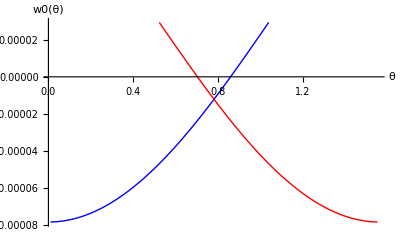

```mathematica
Show[A2,B2,PlotRange->All]
```

### Determinazione di Nm0 [ω]

```mathematica
For[i=0,i≤imax,i++,F[[i+1]]={i δ,Nm0[i δ]}]
```

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

```mathematica
For[i=0,i≤imax,i++,Ft[[i+1]]={i δ+θ0,F[[imax+1-i,2]]}]
```

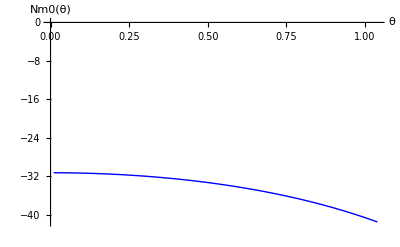

```mathematica
A3=ListLinePlot[{F},AxesOrigin->{0,0},AxesLabel->{"θ","Nm0(θ)"},PlotStyle->{{Blue,Thin}}]
```

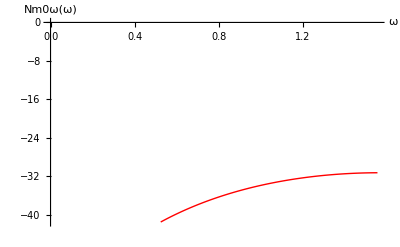

```mathematica
B3=ListLinePlot[{Ft},AxesOrigin->{0,0},AxesLabel->{"ω","Nm0ω(ω)"},PlotStyle->{{Red,Thin}}]
```

```mathematica
Nm0ω=Interpolation[Ft];
```

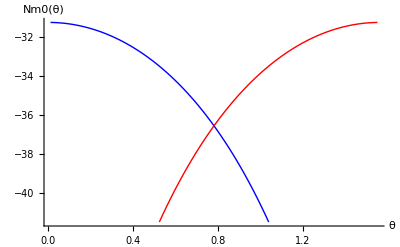

```mathematica
Show[A3,B3,PlotRange->All]
```

### Determinazione di Np0 [ω]

```mathematica
For[i=0,i≤imax,i++,F[[i+1]]={i δ,Np0[i δ]}]
```

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

```mathematica
For[i=0,i≤imax,i++,Ft[[i+1]]={i δ+θ0,F[[imax+1-i,2]]}]
```

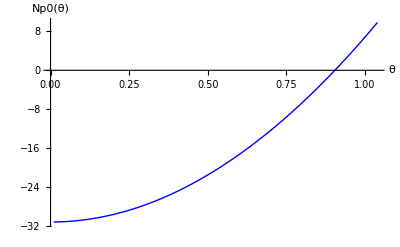

```mathematica
A4=ListLinePlot[{F},AxesOrigin->{0,0},AxesLabel->{"θ","Np0(θ)"},PlotStyle->{{Blue,Thin}}]
```

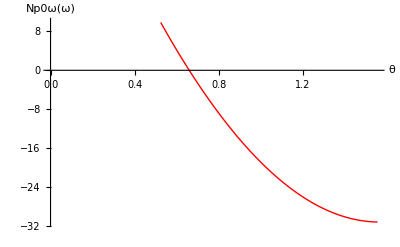

```mathematica
B4=ListLinePlot[{Ft},AxesOrigin->{0,0},AxesLabel->{"θ","Np0ω(ω)"},PlotStyle->{{Red,Thin}}]
```

```mathematica
Np0ω=Interpolation[Ft];
```

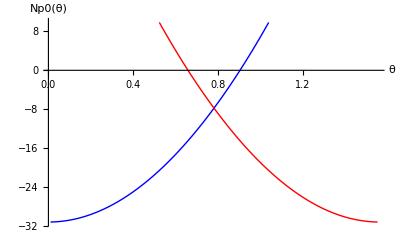

```mathematica
Show[A4,B4,PlotRange->All]
```

### Determinazione di ϵm0 [ω]

```mathematica
For[i=0,i≤imax,i++,F[[i+1]]={i δ,ϵm0[i δ]}]
```

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

```mathematica
For[i=0,i≤imax,i++,Ft[[i+1]]={i δ+θ0,F[[imax+1-i,2]]}]
```

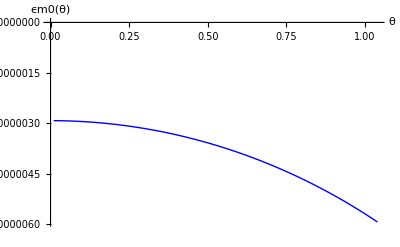

```mathematica
A5=ListLinePlot[{F},AxesOrigin->{0,0},AxesLabel->{"θ","ϵm0(θ)"},PlotStyle->{{Blue,Thin}}]
```

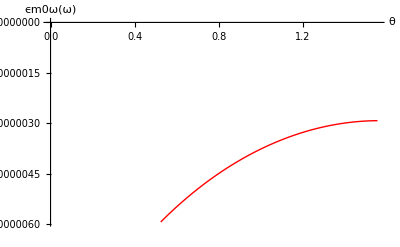

```mathematica
B5=ListLinePlot[{Ft},AxesOrigin->{0,0},AxesLabel->{"θ","ϵm0ω(ω)"},PlotStyle->{{Red,Thin}}]
```

```mathematica
ϵm0ω=Interpolation[Ft];
```

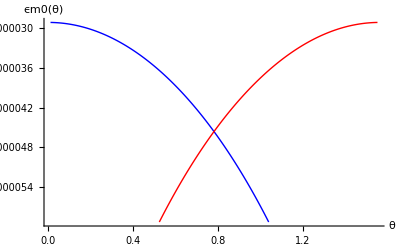

```mathematica
Show[A5,B5,PlotRange->All]
```

### Determinazione di ϵp0 [ω]

```mathematica
For[i=0,i≤imax,i++,F[[i+1]]={i δ,ϵp0[i δ]}]
```

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

```mathematica
For[i=0,i≤imax,i++,Ft[[i+1]]={i δ+θ0,F[[imax+1-i,2]]}]
```

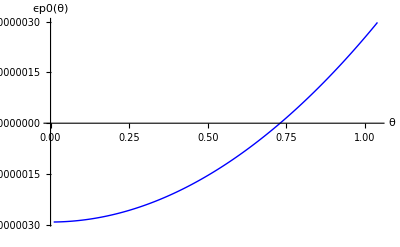

```mathematica
A6=ListLinePlot[{F},AxesOrigin->{0,0},AxesLabel->{"θ","ϵp0(θ)"},PlotStyle->{{Blue,Thin}}]
```

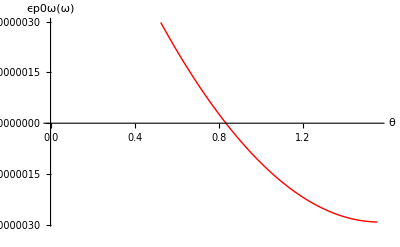

```mathematica
B6=ListLinePlot[{Ft},AxesOrigin->{0,0},AxesLabel->{"θ","ϵp0ω(ω)"},PlotStyle->{{Red,Thin}}]
```

```mathematica
ϵp0ω=Interpolation[Ft];
```

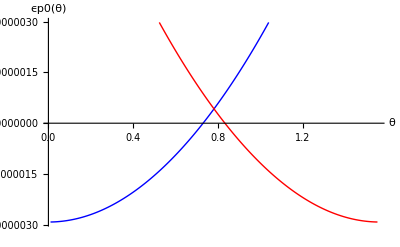

```mathematica
Show[A6,B6,PlotRange->All]
```

### Determinazione di φ0 [ω]

```mathematica
For[i=0,i≤imax,i++,F[[i+1]]={i δ,φ0[i δ]}]
```

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity\ ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0.  + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

```mathematica
For[i=0,i≤imax,i++,Ft[[i+1]]={i δ+θ0,F[[imax+1-i,2]]}]
```

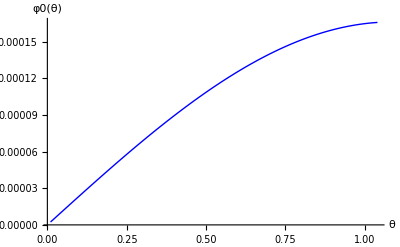

```mathematica
A7=ListLinePlot[{F}, AxesOrigin -> {0, 0}, AxesLabel -> {"θ", "φ0(θ)"}, PlotStyle -> {{Blue, Thin}},PlotRange -> All]
```

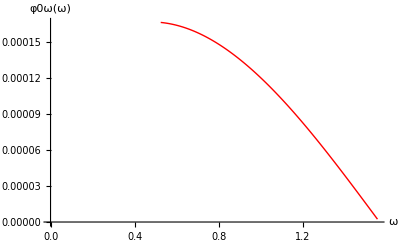

```mathematica
B7=ListLinePlot[{Ft},AxesOrigin->{0,0},AxesLabel->{"ω","φ0ω(ω)"},PlotStyle->{{Red,Thin}}]
```

```mathematica
φ0ω=Interpolation[Ft];
```

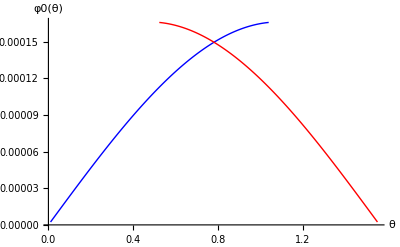

```mathematica
Show[A7,B7]
```

## GRAFICI COMPLETI MEMBRANA IN FUNZIONE DI s

### Spostamento u[s]

```mathematica
Fs1=Table[0,{imax+1},{2}];
```

```mathematica
For[i=0,i≤imax,i++,Fs1[[i+1]]={R i δ+R θ0,u0ω[i δ+θ0]}]
```

```mathematica
us=Interpolation[Fs1];
```

```mathematica
Plot[us[s],{s,R θ0,R α},AxesOrigin->{0,0},PlotStyle->{Blue,Thick},AxesLabel->{"s","u(s)"},PlotRange->All];
```

```mathematica
Plot[-us[s],{s,R θ0,R α},AxesOrigin->{0,0},PlotStyle->{Blue,Thick},AxesLabel->{"s","u(s)"},PlotRange->All];
```

### Spostamento v[s]

```mathematica
Fs2=Table[0,{imax+1},{2}];
```

```mathematica
For[i=0,i≤imax,i++,Fs2[[i+1]]={R i δ+R θ0,w0ω[i δ+θ0]}]
```

```mathematica
vs=Interpolation[Fs2];
```

```mathematica
Plot[vs[s],{s,R θ0,R α},AxesOrigin->{0,0},PlotStyle->{Red,Thick},AxesLabel->{"s","v(s)"},PlotRange->All];
```

```mathematica
vs[R θ0]
```

0.000029361

### Sforzo Normale di meridiano Nm[s]

```mathematica
Fs4=Table[0,{imax+1},{2}];
```

```mathematica
For[i=0,i≤imax,i++,Fs4[[i+1]]={R i δ+R θ0,Nm0ω[i δ+θ0]}]
```

```mathematica
Nms=Interpolation[Fs4];
```

```mathematica
Plot[Nms[s],{s,R θ0,R α},AxesOrigin->{0,0},PlotStyle->{Magenta,Thick},AxesLabel->{"s","Nm(s)"},PlotRange->All];
```

### Sforzo Normale di parallelo Np[s]

```mathematica
Fs5=Table[0,{imax+1},{2}];
```

```mathematica
For[i=1,i≤imax,i++,Fs5[[i+1]]={R i δ+R θ0,Np0ω[i δ+θ0]}]
```

```mathematica
Nps=Interpolation[Fs5];
```

```mathematica
Plot[Nps[s],{s,R θ0,R α},AxesOrigin->{0,0},PlotStyle->{Yellow,Thick},AxesLabel->{"s","Np(s)"},PlotRange->All];
```

## Risoluzione del Problema di Guscio

Incognite iperstatiche H,M

Sapendo che la cupola è vincolata con degli incastri ne consegue che spostamenti e rotazioni in corrispondenza dei vincoli sono nulli. Pertanto si impone la condizione: ξ=φ=0.

Coefficienti di Bordo

```mathematica
d=(EL h^3)/(12(1-ν^2));
```

```mathematica
α1=((EL h)/(4 d R^2))^(1/4);
```

```mathematica
λ=(EL h)/R^2;
```

```mathematica
ξH[θ_]=(2 α1)/λ Sin[θ]^2;
```

```mathematica
ξM[θ_]=(2 α1^2)/λ Sin[θ];
```

```mathematica
φH[θ_]=(2 α1^2)/λ Sin[θ];
```

```mathematica
φM[θ_]=(4 α1^3)/λ;
```

Calcolo dei coefficienti della matrice di flessibilità in θmax=π/2

```mathematica
ξH[θmax]
ξM[θmax]
φH[θmax]
φM[θmax]
```

0.0000162593

0.000015263

0.000015263

0.0000286557

```mathematica
Hm=-Nm0[θmax] Cos[θmax] (*Nm[θmax] o Nm[θ0]?*)
```

20.8333

```mathematica
EQ21=ξH[θmax] (H+Hm)+ξM[θmax] M+ξ0[θmax]==0;
```

```mathematica
EQ22=φH[θmax] (H+Hm)+φM[θmax] M+φ0[θmax]==0;
```

```mathematica
SOL21=Solve[{EQ21,EQ22},{H,M}]
```

{{H→-13.2131,M→-9.85129}}

```mathematica
H=H/.SOL21[[1]]
```

-13.2131

```mathematica
M=M/.SOL21[[1]]
```

-9.85129

```mathematica
θ=π/2-ω;
```

```mathematica
ω0=θ0;
```

```mathematica
β=((EL h R^2)/(4 d))^(1/4);
```

```mathematica
Tm1[ω_]= Exp[-β ω] (c1 Sin[β ω] + c2 Cos[β ω])
```

ⅇ^(-8.12963 ω) (c2 Cos[8.12963 ω]+c1 Sin[8.12963 ω])

```mathematica
Km[ω_]= Tm1'''[ω]/(EL h);
```

```mathematica
φ1[ω_]=Tm1''[ω]/(EL h);
```

```mathematica
Kp[ω_]=(φ1[ω] Cot[θ])/R;
```

```mathematica
Nm1[ω_]=Tm1[ω] Cot[θ];
```

```mathematica
Mm1[ω_]=(EL h^3)/(12(1-ν^2)) Km[ω]+ν (EL h^3)/(12(1-ν^2)) Kp[ω];
```

```mathematica
Mp1[ω_]=ν (EL h^3)/(12(1-ν^2)) Km[ω]+(EL h^3)/(12(1-ν^2)) Kp[ω];
```

Condizioni al contorno

```mathematica
cc21=Tm1[ω0] Cos[ω0]+Nm1[ω0] Sin[θ0]==+(H+Hm)
```

0.0163615 (-0.897942 c1-0.440114 c2)==7.62019

```mathematica
cc22 =Mm1[ω0]==-M;
```

```mathematica
costanti=Solve[{cc21,cc22},{c1,c2}]
```

{{c1→-262.648,c2→-522.355}}

```mathematica
c1=c1/.costanti
```

{-262.648}

```mathematica
c2=c2/.costanti
```

{-522.355}

```mathematica
Tm1[ω_]=Tm1[ω]/.costanti
```

{{ⅇ^(-8.12963 ω) (-522.355 Cos[8.12963 ω]-262.648 Sin[8.12963 ω])}}

```mathematica
Nm1[ω_]=Tm1[ω] Cot[θ]
```

{{ⅇ^(-8.12963 ω) (-522.355 Cos[8.12963 ω]-262.648 Sin[8.12963 ω]) Tan[ω]}}

```mathematica
EQ23=Tm1'[ω]+Tm1[ω] Cot[θ]-(Nm1[ω]-Np1[ω])==0;
```

```mathematica
Np1[ω_]=Np1[ω]/.Solve[EQ23,Np1[ω]][[1]];
```

```mathematica
ϵm1[ω_]=1/(EL h) (Nm1[ω]-ν Np1[ω]);
ϵp1[ω_]=1/(EL h) (Np1[ω]-ν Nm1[ω]);
```

```mathematica
u1[ω_]=Sin [θ](Integrate[ExpandAll[R((ϵm1[ω]-ϵp1[ω])/Sin[θ])],ω]+c3);
```

```mathematica
cc23=u1[ω0]==0;
```

```mathematica
c3=c3/.Solve[cc23,c3][[1]];
```

```mathematica
w1[ω_]=R ϵm1[ω]-u1'[ω];
```

## Grafici Pb di guscio

### Spostamento tangente u1 [ω]

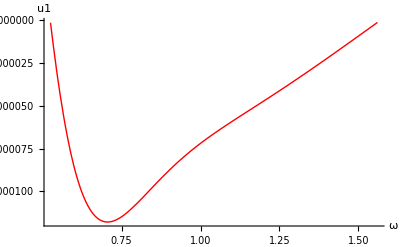

```mathematica
Plot[u1[ω],{ω,θ0,α},AxesOrigin->{0,0},AxesLabel->{"ω","u1"},PlotStyle->{Red,Thick},PlotRange->All]
```

### Spostamento normale w1 [ω]

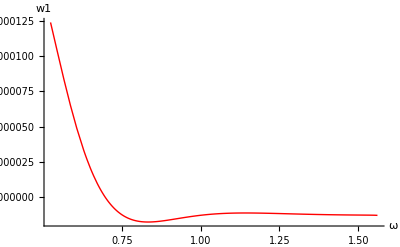

```mathematica
Plot[w1[ω],{ω,θ0,α},AxesOrigin->{0,0},AxesLabel->{"ω","w1"},PlotStyle->{Red,Thick},PlotRange->All]
```

### Rotazione φ1 [ω]

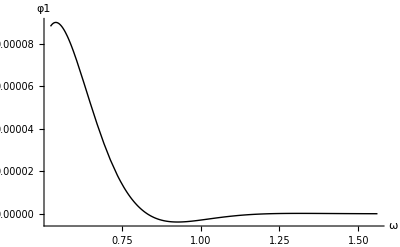

```mathematica
Plot[φ1[ω],{ω,θ0,α},AxesOrigin->{0,0},AxesLabel->{"ω","φ1"},PlotStyle->{Black,Thick},PlotRange->All]
```

### Curvatura flessionale di meridiano km [ω]

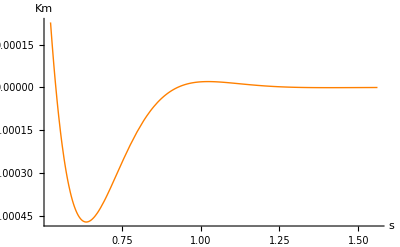

```mathematica
Plot[Km[ω],{ω,θ0,α},AxesOrigin->{0,0},AxesLabel->{"s","Km"},PlotStyle->{Orange,Thick},PlotRange->All]
```

### Curvatura flessionale di meridiano kp [ω]

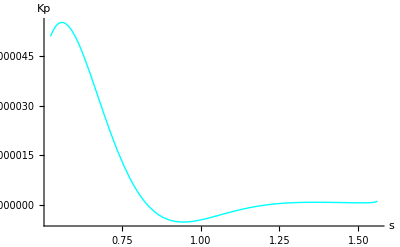

```mathematica
Plot[Kp[ω],{ω,θ0,α},AxesOrigin->{0,0},AxesLabel->{"s","Kp"},PlotStyle->{Cyan,Thick},PlotRange->All]
```

### Sforzo normale di merdiano Nm1 [ω]

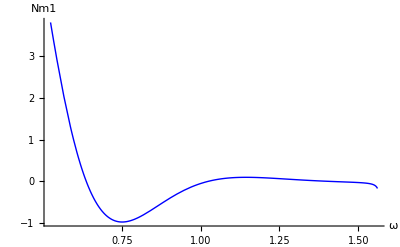

```mathematica
Plot[Nm1[ω],{ω,θ0,α},AxesOrigin->{0,0},AxesLabel->{"ω","Nm1"},PlotStyle->{Blue,Thick},PlotRange->All]
```

### Sforzo normale di parallelo Np1 [ω]

```mathematica
Plot[Np1[ω],{ω,θ0,θ},AxesOrigin->{0,0},AxesLabel->{"ω","Np1"},PlotStyle->{Red,Thick},PlotRange->All]
```

Plot::plln: Limiting value π/2 - ω in {ω, θ0, θ} is not a machine-sized real number.

Plot[Np1[ω],{ω,θ0,θ},AxesOrigin→{0,0},AxesLabel→{ω,Np1},PlotStyle→{Red,Thick},PlotRange→All]

### Taglio di meridiano Tm1 [ω]

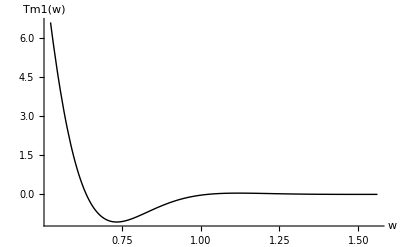

```mathematica
Plot[Tm1[ω],{ω,θ0,α},AxesOrigin->{0,0},AxesLabel->{"w","Tm1(w)"},PlotStyle->{Black,Thick},PlotRange->All]
```

### Momento di merdiano Mm1 [ω]

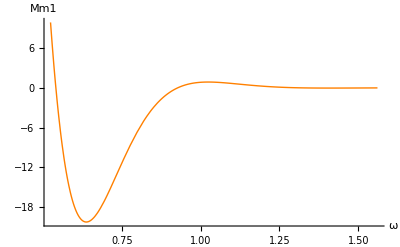

```mathematica
Plot[Mm1[ω],{ω,θ0,α},AxesOrigin->{0,0},AxesLabel->{"ω","Mm1"},PlotStyle->{Orange,Thick},PlotRange->All]
```

### Momento di parallelo Mp1 [ω]

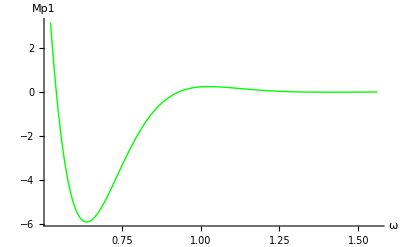

```mathematica
Plot[Mp1[ω],{ω,θ0,α},AxesOrigin->{0,0},AxesLabel->{"ω","Mp1"},PlotStyle->{Green,Thick},PlotRange->All]
```

## GRAFICI COMPLETI (pb di membrana+pb di guscio)

### spostamento u[ω] = u0[ω] + u1[ω]

```mathematica
u[ω_]=u0ω[ω]+u1[ω];
```

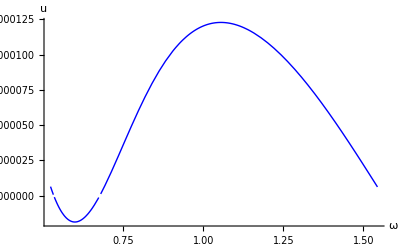

```mathematica
Plot[u0ω[ω]+u1[ω],{ω,θ0,α},AxesOrigin->{0,0},AxesLabel->{"ω","u"},PlotStyle->{Blue,Thick},PlotRange->All]
```

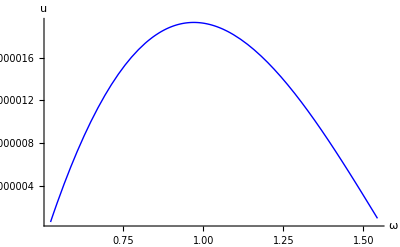

```mathematica
Plot[u0ω[ω],{ω,θ0,α},AxesOrigin->{0,0},AxesLabel->{"ω","u"},PlotStyle->{Blue,Thick},PlotRange->All]
```

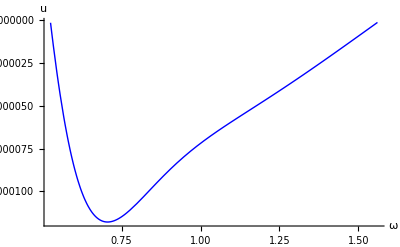

```mathematica
Plot[u1[ω],{ω,θ0,α},AxesOrigin->{0,0},AxesLabel->{"ω","u"},PlotStyle->{Blue,Thick},PlotRange->All]
```

### spostamento w[ω] = w0[ω] + w1[ω]

```mathematica
w[ω_]=w0ω[ω]+w1[ω];
```

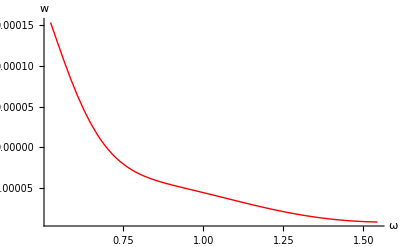

```mathematica
Plot[w[ω],{ω,θ0,α},AxesOrigin->{0,0},AxesLabel->{"ω","w"},PlotStyle->{Red,Thick},PlotRange->All]
```

### Rotazione φ1[ω]

```mathematica
φ[ω_]=-φ0ω[ω]+φ1[ω];
```

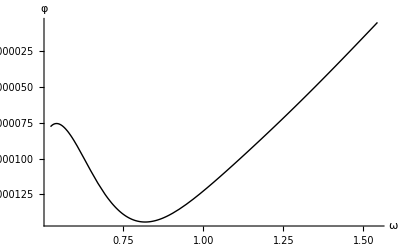

```mathematica
Plot[φ[ω],{ω,θ0,α},AxesOrigin->{0,0},AxesLabel->{"ω","φ"},PlotStyle->{Black,Thick},PlotRange->All]
```

### Curvatura flessionale di meridiano km [ω]

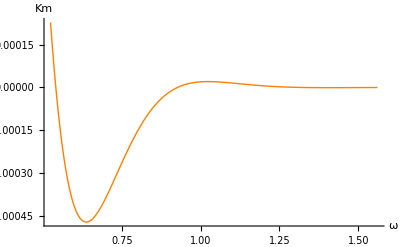

```mathematica
Plot[Km[ω],{ω,θ0,α},AxesOrigin->{0,0},AxesLabel->{"ω","Km"},PlotStyle->{Orange,Thick},PlotRange->All]
```

### Curvatura flessionale di meridiano km [ω]

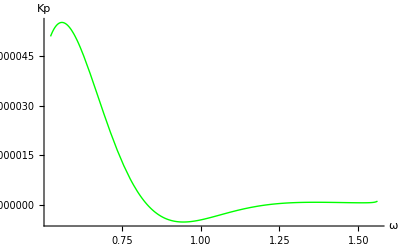

```mathematica
Plot[Kp[ω],{ω,θ0,α},AxesOrigin->{0,0},AxesLabel->{"ω","Kp"},PlotStyle->{Green,Thick},PlotRange->All]
```

### Sforzo Normale di meridiano Nm[ω] = Nm0[ω] + Nm1[ω]

```mathematica
Nm[ω_]=Nm0ω[ω]+Nm1[ω];
```

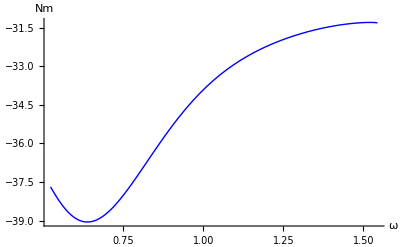

```mathematica
Plot[Nm[ω],{ω,θ0,α},AxesOrigin->{0,0},AxesLabel->{"ω","Nm"},PlotStyle->{Blue,Thick},PlotRange->All]
```

### Sforzo Normale di parallelo Np[ω] = Np0[ω] + Np1[ω]

```mathematica
Np[ω_]=Np0ω[ω]+Np1[ω];
```

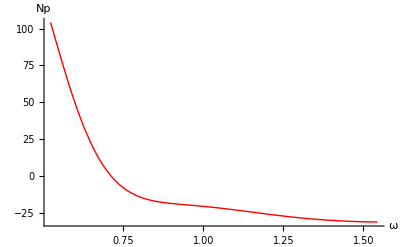

```mathematica
Plot[Np0ω[ω]+Np1[ω],{ω,θ0,α},AxesOrigin->{0,0},AxesLabel->{"ω","Np"},PlotStyle->{Red,Thick},PlotRange->All]
```

### Taglio di meridiano Tm [ω]

```mathematica
Plot[Tm1[ω],{ω,θ0,α},AxesOrigin->{0,0},AxesLabel->{"w","Tm1(w)"},PlotStyle->{Black,Thick},PlotRange->All]
```

-Graphics-

### Momento di merdiano Mm [ω]

```mathematica
Plot[Mm1[ω],{ω,θ0,α},AxesOrigin->{0,0},AxesLabel->{"ω","Mm1"},PlotStyle->{Orange,Thick},PlotRange->All]
```

-Graphics-

### Momento di parallelo Mp [ω]

```mathematica
Plot[Mp1[ω],{ω,θ0,α},AxesOrigin->{0,0},AxesLabel->{"ω","Mp1"},PlotStyle->{Green,Thick},PlotRange->All]
```

-Graphics-

## GRAFICI COMPLETI DI GECKELER IN FUNZIONE DI s

### Spostamento u[s]

```mathematica
Fs1=Table[0,{imax+1},{2}];
```

```mathematica
For[i=0,i≤imax,i++,Fs1[[i+1]]={R i δ+R θ0,u[i δ+θ0]}]
```

```mathematica
uss=Interpolation[Fs1];
```

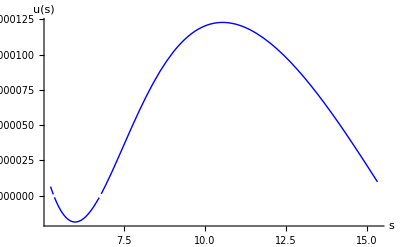

```mathematica
Plot[uss[s],{s,R θ0,R α},AxesOrigin->{0,0},PlotStyle->{Blue,Thick},AxesLabel->{"s","u(s)"},PlotRange->All]
```

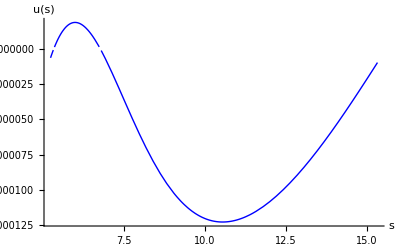

```mathematica
C1=Plot[-uss[s],{s,R θ0,R α},AxesOrigin->{0,0},PlotStyle->{Blue,Thick},AxesLabel->{"s","u(s)"},PlotRange->All]
```

### Spostamento v[s]

```mathematica
Fs2=Table[0,{imax+1},{2}];
```

```mathematica
For[i=0,i≤imax,i++,Fs2[[i+1]]={R i δ+R θ0,w[i δ+θ0]}]
```

```mathematica
vss=Interpolation[Fs2];
```

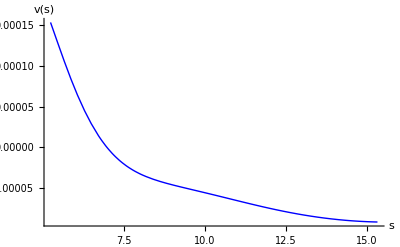

```mathematica
C2=Plot[vss[s],{s,R θ0,R α},AxesOrigin->{0,0},PlotStyle->{Blue,Thick},AxesLabel->{"s","v(s)"},PlotRange->All]
```

### Rotazione φ[s]

```mathematica
Fs3=Table[0,{imax+1},{2}];
```

```mathematica
For[i=0,i≤imax,i++,Fs3[[i+1]]={R i δ+R θ0,φ[i δ+θ0]}]
```

```mathematica
φss=Interpolation[Fs3];
```

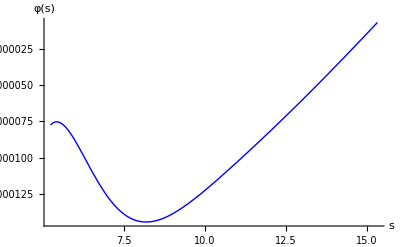

```mathematica
C3=Plot[φss[s],{s,R θ0,R α},AxesOrigin->{0,0},PlotStyle->{Blue,Thick},AxesLabel->{"s","φ(s)"},PlotRange->All]
```

### Sforzo Normale di meridiano Nm[s]

```mathematica
Fs4=Table[0,{imax+1},{2}];
```

```mathematica
For[i=0,i≤imax,i++,Fs4[[i+1]]={R i δ+R θ0,Nm[i δ+θ0]}]
```

```mathematica
Nmss=Interpolation[Fs4];
```

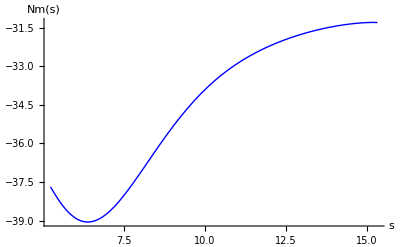

```mathematica
C4=Plot[Nmss[s],{s,R θ0,R α},AxesOrigin->{0,0},PlotStyle->{Blue,Thick},AxesLabel->{"s","Nm(s)"},PlotRange->All]
```

### Sforzo Normale di parallelo Np[s]

```mathematica
Fs5=Table[0,{imax+1},{2}];
```

```mathematica
For[i=1,i≤imax,i++,Fs5[[i+1]]={R i δ+R θ0,Np[i δ+θ0]}]
```

```mathematica
Npss=Interpolation[Fs5];
```

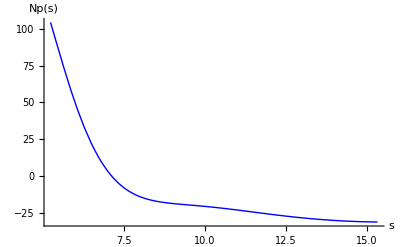

```mathematica
C5=Plot[Npss[s],{s,R θ0,R α},AxesOrigin->{0,0},PlotStyle->{Blue,Thick},AxesLabel->{"s","Np(s)"},PlotRange->All]
```

### Taglio di meridiano Tm[s]

```mathematica
Fs6=Table[0,{imax+1},{2}];
```

```mathematica
For[i=0,i≤imax,i++,Fs6[[i+1]]={R i δ+R θ0,Tm1[i δ+θ0]}]
```

```mathematica
Tmss=Interpolation[Fs6];
```

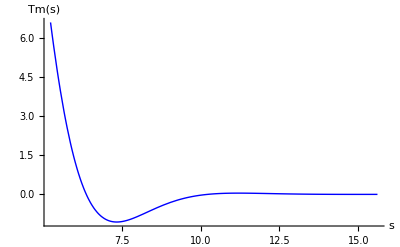

```mathematica
C6=Plot[Tmss[s],{s,R θ0,R α},AxesOrigin->{0,0},PlotStyle->{Blue,Thick},AxesLabel->{"s","Tm(s)"},PlotRange->All]
```

### Momento di meridiano Mm[s]

```mathematica
Fs7=Table[0,{imax+1},{2}];
```

```mathematica
For[i=0,i≤imax,i++,Fs7[[i+1]]={R i δ+R θ0,Mm1[i δ+θ0]}]
```

```mathematica
Mm1ss=Interpolation[Fs7];
```

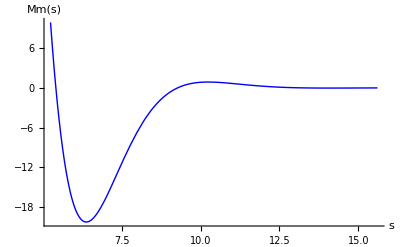

```mathematica
C7=Plot[Mm1ss[s],{s,R θ0,R α},AxesOrigin->{0,0},PlotStyle->{Blue,Thick},AxesLabel->{"s","Mm(s)"},PlotRange->All]
```

### Momento di parallelo Mp[s]

```mathematica
Fs8=Table[0,{imax+1},{2}];
```

```mathematica
For[i=0,i≤imax,i++,Fs8[[i+1]]={R i δ+R θ0,Mp1[i δ+θ0]}]
```

```mathematica
Mp1ss=Interpolation[Fs8];
```

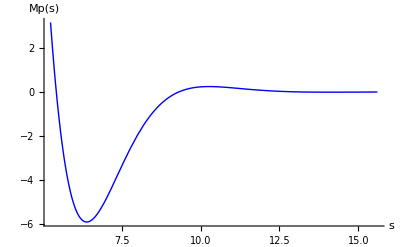

```mathematica
Plot[Mp1ss[s],{s,R θ0,R α},AxesOrigin->{0,0},PlotStyle->{Blue,Thick},AxesLabel->{"s","Mp(s)"},PlotRange->All]
```

## CILINDRO

```mathematica
β=((3(1-ν^2))/(R^2 h^2))^(1/4);
```

```mathematica
v4[s_]=ⅇ^(-β s)(Subscript[c, 1] Sin[β s]+Subscript[c, 2] Cos[β s])+ⅇ^(β s)(Subscript[c, 3] Sin[β s]+Subscript[c, 4] Cos[β s]);
```

```mathematica
u4[s_]=Subscript[c, 6]+s Subscript[c, 7];
```

#### Equazioni di congruenza

```mathematica
ϵm4[s_]=u4'[s];
φ4[s_]=v4'[s];
κm4[s_]=φ4'[s];
ϵp4[s_]=v4[s]/r2[s];
```

#### Legame

```mathematica
Nm4[s_]=EA ϵm4[s];
```

```mathematica
Tm4[s_]=-Mm4'[s];
```

```mathematica
Mm4[s_]=El κm4[s];
```

```mathematica
Np4[s_]= +EA ϵp4[s];
```

```mathematica
ccc1=φ4[R α0]==0;
ccc2=Tm4[R α0]-FF==0;
ccc3=φ4[R α]==0;
ccc4=v4[R α]==0;
ccc5=v4[R α0]==-vs[R α0];
ccc6=u4[R α]==0;
ccc7=u4[R α0]==0;
```

```mathematica
COSTT=NSolve[{ccc1,ccc2,ccc3,ccc4,ccc5},{Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],FF,Subscript[c, 6],Subscript[c, 7]}];
```

```mathematica
v4[s_]=v4[s]/.COSTT[[1]];
```

```mathematica
u4[s_]=u4[s]/.COSTT[[1]];
```

#### Equazioni di congruenza

```mathematica
ϵm4[s_]=u4'[s];
φ4[s_]=v4'[s];
κm4[s_]=φ4'[s];
ϵp4[s_]=v4[s]/r2[s];
```

#### Legame

```mathematica
Nm4[s_]=EA ϵm4[s];
```

```mathematica
Mm4[s_]=El κm4[s];
```

```mathematica
Tm4[s_]=-Mm4'[s];
```

```mathematica
Np4[s_]= EA ϵp4[s];
```

```mathematica
A1=Plot[-us[s],{s,R α0,R α},PlotStyle->{Red,Thick},PlotRange-> All,AxesOrigin->{R α0,0}];
```

```mathematica
A2=Plot[v4[s]+vs[s],{s,R α0,R α},PlotStyle->{Red,Thick},PlotRange-> All,AxesOrigin->{R α0,0}];
```

```mathematica
A3=Plot[φ4[s],{s,R α0,R α},PlotStyle->{Red,Thick},PlotRange-> All,AxesOrigin->{R α0,0}];
```

```mathematica
A7=Plot[Mm4[s],{s,R α0,R α},PlotStyle->{Red,Thick},PlotRange-> All,AxesOrigin->{R α0,0}];
```

```mathematica
A6=Plot[Tm4[s],{s,R α0,R α},PlotStyle->{Red,Thick},PlotRange-> All,AxesOrigin->{R α0,0}];
```

```mathematica
A4=Plot[Nms[s],{s,R α0,R α},PlotStyle->{Red,Thick},PlotRange-> All,AxesOrigin->{R α0,0}];
```

```mathematica
A5=Plot[Np4[s]+Nps[s],{s,R α0,R α},PlotStyle->{Red,Thick},PlotRange-> All,AxesOrigin->{R α0,0}];
```

## Modello Inestensibile

#### Equazioni di congruenza

```mathematica
v10[s_]=-R u10'[s];
φ10[s_]=v10'[s]-u10[s]/R;
κm10[s_]=φ10'[s];
ϵp10[s_]=v10[s]/R;
```

#### Legame

```mathematica
Nm10[s_]=R(P Sin[s/R]+Tm10'[s]-Np10[s]/R)+ν EA ϵp10[s];
```

```mathematica
Tm10[s_]=-Mm10'[s];
```

```mathematica
Mm10[s_]=El κm10[s];
```

```mathematica
Np10[s_]= +EA ϵp10[s]+ν R(P Sin[s/R]+Tm10'[s]-Np10[s]/R);
```

```mathematica
cccc1=u10[R α0]==0;
cccc2=v10[R α0]==0;
cccc3=φ10[R α0]==0;
cccc4=u10[R α]==0;
cccc5=Tm10[R α]==0;
cccc6=φ10[R α]==0;
```

```mathematica
COSTTT=NSolve[{cccc1,cccc2,cccc3,cccc4,cccc5,cccc6},{C[1],C[2],C[3],C[4],C[5],C[6]}]
```

{{C[1]→-1.59266×10^-14-6.51897×10^-15 ⅈ,C[2]→-0.0002653-0.000146915 ⅈ,C[3]→-1.59266×10^-14+6.51897×10^-15 ⅈ,C[4]→-0.0002653+0.000146915 ⅈ,C[5]→0.000205323-2.1788×10^-21 ⅈ,C[6]→-0.0000130579+1.39558×10^-22 ⅈ}}

```mathematica
u10[s_]=u10[s]/.COSTTT[[1]];
```

#### Equazioni di congruenza

```mathematica
v10[s_]=-R u10'[s];
φ10[s_]=v10'[s]-u10[s]/R;
κm10[s_]=φ10'[s];
ϵp10[s_]=v10[s]/R;
```

#### Legame

```mathematica
Mm10[s_]=El κm10[s];
```

```mathematica
Tm10[s_]=-Mm10'[s];
```

```mathematica
Np10[s_]= +EA ϵp10[s];
```

```mathematica
Nm10[s_]=R(P Sin[s/R]+Tm10'[s]-Np10[s]/R)+ν EA ϵp10[s];
```

```mathematica
Np10[s_]= +EA ϵp10[s]+ν R(P Sin[s/R]+Tm10'[s]-Np10[s]/R);
```

```mathematica
Nm10[s_]=R(P Sin[s/R]+Tm10'[s]-Np10[s]/R)+ν EA ϵp10[s];
```

```mathematica
BB1=Plot[Re[u10[s]],{s,R α0,R α},PlotStyle->{Green,Thick},PlotRange-> All];
```

```mathematica
BB2=Plot[Re[v10[s]],{s,R α0,R α},PlotStyle->{Green,Thick},PlotRange-> All];
```

```mathematica
BB3=Plot[Re[φ10[s]],{s,R α0,R α},PlotStyle->{Green,Thick},PlotRange-> All];
```

```mathematica
BB7=Plot[Re[Mm10[s]],{s,R α0,R α},PlotStyle->{Green,Thick},PlotRange-> All];
```

```mathematica
BB6=Plot[Re[Tm10[s]],{s,R α0,R α},PlotStyle->{Green,Thick},PlotRange-> All];
```

```mathematica
BB4=Plot[Re[Nm10[s]],{s,R α0,R α},PlotStyle->{Green,Thick},PlotRange-> All];
```

```mathematica
BB5=Plot[Re[Np10[s]],{s,R α0,R α},PlotStyle->{Green,Thick},PlotRange-> All];
```

## EQUAZIONI MIE NON INESTENSIBILI

#### Equazioni di congruenza

```mathematica
ϵm6[s_]=u6'[s]+v6[s]/r1[s];
φ6[s_]=v6'[s]-u6[s]/r1[s];
κm6[s_]=φ6'[s];
ϵp6[s_]=v6[s]/r2[s];
```

#### Legame

```mathematica
Nm6[s_]=EA ϵm6[s]+ν EA ϵp6[s];
```

```mathematica
Tm6[s_]=-Mm6'[s];
```

```mathematica
Mm6[s_]=El κm6[s];
```

```mathematica
Np6[s_]= +EA ϵp6[s]+ν EA ϵm6[s];
```

```mathematica
ccc1=u6[R α0]==0;
ccc2=v6[R α0]==0;
ccc3=φ6[R α0]==0;
ccc4=u6[R α]==0;
ccc5=Tm6[R α]==0;
ccc6=φ6[R α]==0;
```

```mathematica
COSTT=NSolve[{ccc1,ccc2,ccc3,ccc4,ccc5,ccc6},{C[1],C[2],C[3],C[4],C[5],C[6]}];
```

```mathematica
u6[s_]=u6[s]/.COSTT[[1]];
```

```mathematica
v6[s_]=v6[s]/.COSTT[[1]];
```

#### Equazioni di congruenza

```mathematica
ϵm6[s_]=u6'[s]+v6[s]/r1[s];
φ6[s_]=v6'[s]-u6[s]/r1[s];
κm6[s_]=φ6'[s];
ϵp6[s_]=v6[s]/r2[s];
```

#### Legame

```mathematica
Nm6[s_]=EA ϵm6[s]+ν EA ϵp6[s];
```

```mathematica
Mm6[s_]=El κm6[s];
```

```mathematica
Tm6[s_]=-Mm6'[s];
```

```mathematica
Np6[s_]= +EA ϵp6[s]+ν EA ϵm6[s];
```

```mathematica
B1=Plot[u6[s],{s,R α0,R α},PlotStyle->{Orange,Thick},PlotRange-> All];
```

```mathematica
B2=Plot[v6[s],{s,R α0,R α},PlotStyle->{Orange,Thick},PlotRange-> All];
```

```mathematica
B3=Plot[φ6[s],{s,R α0,R α},PlotStyle->{Orange,Thick},PlotRange-> All];
```

```mathematica
B7=Plot[Mm6[s],{s,R α0,R α},PlotStyle->{Orange,Thick},PlotRange-> All];
```

```mathematica
B6=Plot[Tm6[s],{s,R α0,R α},PlotStyle->{Orange,Thick},PlotRange-> All];
```

```mathematica
B4=Plot[Nm6[s],{s,R α0,R α},PlotStyle->{Orange,Thick},PlotRange-> All];
```

```mathematica
B5=Plot[Np6[s],{s,R α0,R α},PlotStyle->{Orange,Thick},PlotRange-> All];
```

## GRAFICI

### Spostamento u[s]

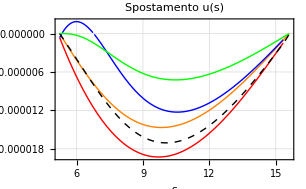

```mathematica
Show[A1,B1,C1,G1,BB1,PlotRange->All,PlotLabel->"Spostamento u(s)",AxesLabel->{"s","u(s)"},AxesOrigin->{R α0,0}, PlotLabel->{"Membrana","s","a","b"},GridLines->Automatic,Frame->True]
```

### Spostamento v[s]

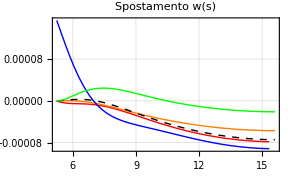

```mathematica
Show[A2,B2,C2,G2,BB2,PlotRange->All,PlotLabel->"Spostamento w(s)",AxesLabel->{"s","w(s)"},AxesOrigin->{R α0,0},GridLines->Automatic,Frame->True]
```

### Rotazione φ[s]

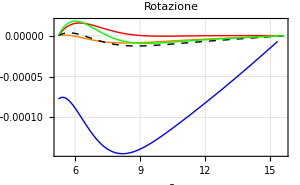

```mathematica
Show[A3,B3,C3,G3,BB3,PlotRange->All,PlotLabel->"Rotazione",AxesLabel->{"s","φ(s)"},AxesOrigin->{R α0,0},GridLines->Automatic,Frame->True]
```

### Taglio di meridiano Tm [s]

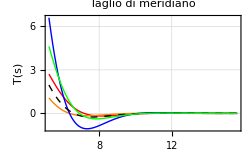

```mathematica
Show[A6,B6,C6,G6,BB6,PlotRange->All,PlotLabel->"Taglio di meridiano",AxesLabel->{"s","T(s)"},AxesOrigin->{R α0,0},GridLines->Automatic,Frame->True]
```

### Momento flettente di meridiano Mm [s]

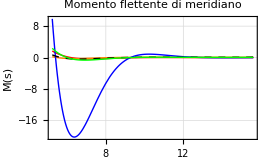

```mathematica
Show[A7,B7,C7,G7,BB7,PlotRange->All,PlotLabel->"Momento flettente di meridiano",AxesLabel->{"s","M(s)"},AxesOrigin->{R α0,0},GridLines->Automatic,Frame->True]
```

### Sforzo Normale di meridiano Nm[s]

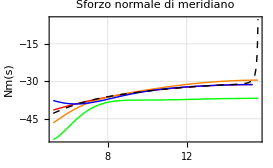

```mathematica
Show[A4,B4,C4,G4,BB4,PlotRange->All,PlotLabel->"Sforzo normale di meridiano",AxesLabel->{"s","Nm(s)"},AxesOrigin->{R α0,0},GridLines->Automatic,Frame->True]
```

### Sforzo Normale circonferenziale Nc[s]

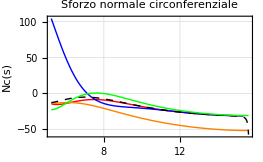

```mathematica
Show[A5,B5,C5,G5,BB5,PlotRange->All,PlotLabel->"Sforzo normale circonferenziale",AxesLabel->{"s","Nc(s)"},AxesOrigin->{R α0,0},GridLines->Automatic,Frame->True]
```